```mathematica
data = Import["/net/home/f09/bajennissen/research/DAY182_cloudy/sec_int_data/778nm.dat"]
```

{{1.83648,-0.126493},{1.67469,-0.0814162},{1.55096,-0.11044},{1.77833,-0.0953442},{1.08395,-0.00698433},{1.0884,1.36581},{1.10777,-0.0949263},{1.1184,-0.040395},{1.90886,-0.140769}}

0.972997-0.615153 x

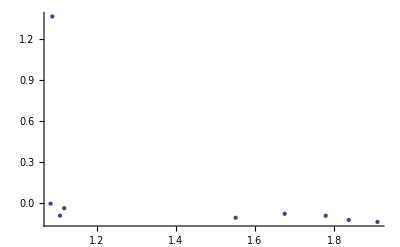

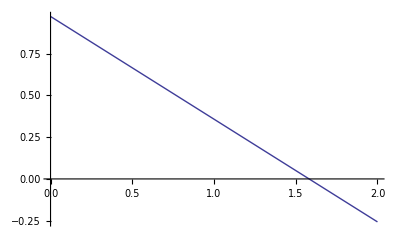

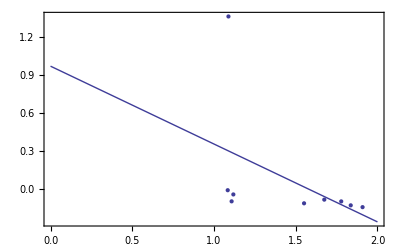

```mathematica
line = Fit[data,{1,x},x]
DataPlot=ListPlot[data]
FitPlot=Plot[line,{x,0,2}]
Show[DataPlot,FitPlot,PlotRange->All,Frame->True,AxesOrigin->{0,0}]
```